```mathematica
SetDirectory[NotebookDirectory[]];

data1 = Import["P1_f4Table1_FUNC1_GAUSS.txt","TABLE"];
data2 = Import["P2_f4Table1_FUNC1_GAUSS.txt","TABLE"];
data3 = Import["P3_f4Table1_FUNC1_GAUSS.txt","TABLE"];
data4 = Import["P4_f4Table1_FUNC1_GAUSS.txt","TABLE"];

xcord=1;
ycord=4 ;
cerror=3;
ctasas=4;

data11=Table[{data1[[i,cerror]],data1[[i,ctasas]]},{i,1,Length[data1],1}];
data12=Table[{data2[[i,cerror]],data2[[i,ctasas]]},{i,1,Length[data2],1}];
data13=Table[{data3[[i,cerror]],data3[[i,ctasas]]},{i,1,Length[data3],1}];
data14=Table[{data4[[i,cerror]],data4[[i,ctasas]]},{i,1,Length[data4],1}];

data1ToPlot = Table[{data1[[i,xcord]],data1[[i,ycord]]},{i,1,Length[data1],1}];
data2ToPlot = Table[{data2[[i,xcord]],data2[[i,ycord]]},{i,1,Length[data2],1}];
data3ToPlot = Table[{data3[[i,xcord]],data3[[i,ycord]]},{i,1,Length[data3],1}];
data4ToPlot = Table[{data4[[i,xcord]],data4[[i,ycord]]},{i,1,Length[data4],1}];
colors = {{Red},{Blue}, {Green}, {Black}};
colors1 = {{Red,Dashed},{Blue,Dashed}, {Green,Dashed}, {Brown,Dashed}};
namestoplot={Style["Func 1",12],Style["M. Simpson 1/3",12],Style["M. Simpson 3/8",12],Style["M. Gauss Legendre",12]};
format = {PlotStyle->colors,PlotLegends->namestoplot,Frame->True,FrameLabel->{"p","Log erro"} ,FrameStyle->Directive[Black, Thickness[0.005],Bold,FontSize->16],FrameTicksStyle->{{FontSize->15,Black},{FontSize->15,Black},{FontSize->15,Black},{FontSize->15,Black}},GridLines->Automatic};
```

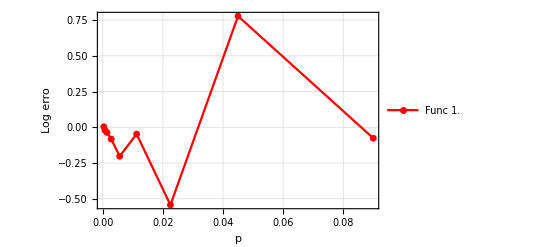

P1_F1_TASA.pdf

```mathematica
plot1 = ListPlot[{data1ToPlot},Joined->True, PlotRange->All,format, PlotMarkers->{Automatic, Small}]
Export["P1_F1_TASA.pdf",plot1]
(*Export["F3_TRAPECIOS.xlsx",data11]
Export["F3_SIMP_1_3.xlsx",data12]
Export["F3_SIMP_3_8.xlsx",data13]
Export["F3_GAUSS.xlsx",data14]*)
```

```mathematica
data1ToPlot
data2ToPlot
data3ToPlot
data4ToPlot
```

{{0.09,-0.076459},{0.045,0.77787},{0.0225,-0.54339},{0.01125,-0.047557},{0.005625,-0.20305},{0.0028125,-0.082535},{0.0014063,-0.03615},{0.00070313,-0.020957},{0.00035156,0.0038343}}

{{-2.4079,-0.076459},{-3.1011,0.77787},{-3.7942,-0.54339},{-4.4874,-0.047557},{-5.1805,-0.20305},{-5.8737,-0.082535},{-6.5668,-0.03615},{-7.26,-0.020957},{-7.9531,0.0038343}}

{{-2.4079,-0.076459},{-3.1011,0.77787},{-3.7942,-0.54339},{-4.4874,-0.047557},{-5.1805,-0.20305},{-5.8737,-0.082535},{-6.5668,-0.03615},{-7.26,-0.020957},{-7.9531,0}}

{{-2.4079,-0.076459},{-3.1011,0.77787},{-3.7942,-0.54339},{-4.4874,-0.047557},{-5.1805,-0.20305},{-5.8737,-0.082535},{-6.5668,-0.03615},{-7.26,-0.020957},{-7.9531,1.2943×10^171}}